## Function definitions

```mathematica
currentsI = {0.5,1,2,3,4,5}/1000;
```

```mathematica
areaElectrode = 0.07;
```

```mathematica
makeIvList[originalList_]:=originalList[[2;;All]];
```

```mathematica
changeTomA[ivList_]:= Transpose@({1,1000}*Transpose@ivList);
```

```mathematica
findMeanCP[allcp_]:= Map[Mean,allcp[[All,All,2]]];
```

```mathematica
findErrCP[allcp_]:= Map[StandardDeviation,allcp[[All,All,2]]];
```

```mathematica
makeCPdata[meancp_]:= Transpose[{Log10[currentsI/areaElectrode],meancp}];
```

```mathematica
modelFitCP[cpdata_,cperr_]:= LinearModelFit[cpdata, x,x,Weights->1/(cperr^2),VarianceEstimatorFunction->(1&)];
```

```mathematica
addErrorInY[xy_,erry_]:= Transpose@{xy[[All,1]],Map[Apply[Around,#]&,Transpose[{xy[[All,2]],erry}]]};
```

```mathematica
extractFitParamters[lineModel_]:=Map[Apply[Around,#]&,lineModel["ParameterTable"][[1,1,2;;3,2;;3]]];
```

```mathematica
makeFitExpression[paramtersFit_]:= paramtersFit[[1]]+x paramtersFit[[2]];
```

## Ni/Fe depositions

### 09/25

LSV

```mathematica
iVsVFeNiDep0925 = changeTomA@makeIvList@(Import["/Users/alimalasmari/Desktop/Ali Alasmari mod8 Fall2023/Archive  20230925_151912 (0001)/LSV Experiment Fe_Ni deposition/Voltammogram/Current vs Potential.csv"]);
```

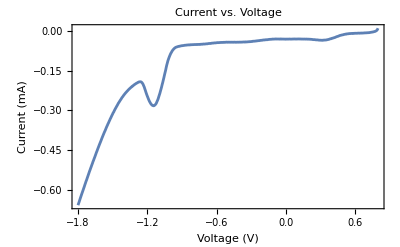

```mathematica
ListLinePlot[iVsVFeNiDep0925,Frame->True,PlotLabel-> "Current vs. Voltage",FrameLabel->{"Voltage (V)","Current (mA)"}]
```

```mathematica
Mean
```

Mean

Deposition at -1.5V

```mathematica
depositionFeNi0925 = makeIvList@Import["/Users/alimalasmari/Desktop/Ali Alasmari mod8 Fall2023/Archive  20230925_151912 (0001)/BE Experiment Fe_Ni deposition/Electrolysis/Measured Current.csv"];
```

```mathematica
depositionFeNi0925=Transpose@({1,1000}*Transpose@depositionFeNi0925);
```

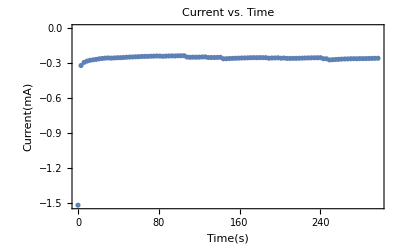

```mathematica
ListPlot[depositionFeNi0925,PlotRange->{All,{All,0}},PlotLabel->"Current vs. Time",Frame->True,FrameLabel->{"Time(s)","Current(mA)"}]
```

Finding total charge transferred to the solution

```mathematica
Mean[depositionFeNi0925[[All,2]]]*300
```

-80.1446

### 09/27

LSV

```mathematica
iVsVFeNiDep0927 = changeTomA@makeIvList@(Import["/Users/alimalasmari/Desktop/Ali Alasmari mod8 Fall2023/Archive  20230927_140401 (0029)/LSV Experiment Fe_Ni deposition/Voltammogram/Current vs Potential.csv"]);
```

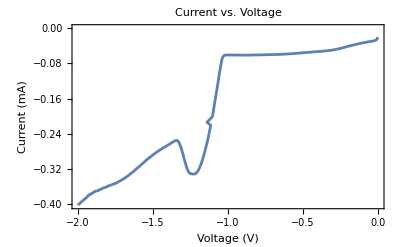

```mathematica
ListLinePlot[iVsVFeNiDep0927,Frame->True,PlotLabel-> "Current vs. Voltage",FrameLabel->{"Voltage (V)","Current (mA)"}]
```

Deposition at -1.5V

```mathematica
depositionFeNi0927= makeIvList@Import["/Users/alimalasmari/Desktop/Ali Alasmari mod8 Fall2023/Archive  20230927_140401 (0029)/BE Experiment Fe_Ni deposition 2/Electrolysis/Measured Current.csv"];
```

```mathematica
depositionFeNi0927=Transpose@({1,1000}*Transpose@depositionFeNi0927);
```

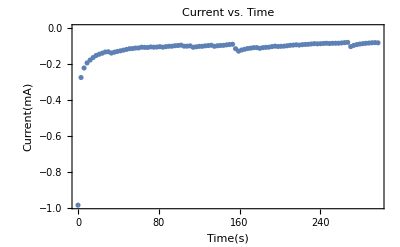

```mathematica
ListPlot[depositionFeNi0927,PlotRange->{All,{All,0}},PlotLabel->"Current vs. Time",Frame->True,FrameLabel->{"Time(s)","Current(mA)"}]
```

Finding total charge transferred to the solution

```mathematica
Mean[depositionFeNi0927[[All,2]]]*300
```

-34.6649

## Glassy Carbon

#### CV

```mathematica
iVsV= Import["/Users/alimalasmari/Desktop/Ali Alasmari mod8 Fall2023/Archive  20230920_143020 (0001)/CV Experimentglassy carbon OER/experiment/results/Current vs Potential.csv"];
```

```mathematica
iVsV0 = changeTomA@makeIvList[iVsV];
```

```mathematica
iVsV0//Dimensions
```

{600,2}

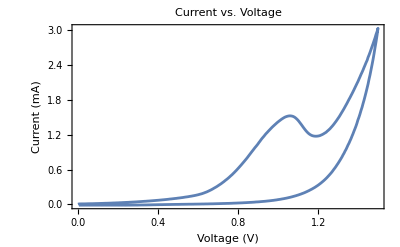

```mathematica
cvgc=ListLinePlot[iVsV0,Frame->True,PlotLabel-> "Current vs. Voltage",FrameLabel->{"Voltage (V)","Current (mA)"}]
```

#### CP

point 52 marks 15s mark which will be used as a point of stability

```mathematica
cp05GlassyCarbon=Import["/Users/alimalasmari/Desktop/Ali Alasmari mod8 Fall2023/Archive  20230920_143020 (0001)/CP Experiment 0.5 mA glassy carbon/Chronopotentiogram/Measured Potential.csv"][[52;;All]];
```

```mathematica
iMesured05GlassyCarbon = Import["/Users/alimalasmari/Desktop/Ali Alasmari mod8 Fall2023/Archive  20230920_143020 (0001)/CP Experiment 0.5 mA glassy carbon/experiment/results/Measured Current.csv"][[52;;All]];
```

```mathematica
cp1GlassyCarbon = Import["/Users/alimalasmari/Desktop/Ali Alasmari mod8 Fall2023/Archive  20230920_143020 (0001)/CP Experiment 1 mA glassy carbon/Chronopotentiogram/Measured Potential.csv"][[52;;All]];
```

```mathematica
iMesured1GlassyCarbon = Import["/Users/alimalasmari/Desktop/Ali Alasmari mod8 Fall2023/Archive  20230920_143020 (0001)/CP Experiment 1 mA glassy carbon/experiment/results/Measured Current.csv"][[52;;All]];
```

```mathematica
cp2GlassyCarbon = Import["/Users/alimalasmari/Desktop/Ali Alasmari mod8 Fall2023/Archive  20230920_143020 (0001)/CP Experiment 2 mA glassy carbon/Chronopotentiogram/Measured Potential.csv"][[52;;All]];
```

```mathematica
iMesured2GlassyCarbon = Import["/Users/alimalasmari/Desktop/Ali Alasmari mod8 Fall2023/Archive  20230920_143020 (0001)/CP Experiment 2 mA glassy carbon/experiment/results/Measured Current.csv"][[52;;All]];
```

```mathematica
cp3GlassyCarbon = Import["/Users/alimalasmari/Desktop/Ali Alasmari mod8 Fall2023/Archive  20230920_143020 (0001)/CP Experiment 3 mA glassy carbon/Chronopotentiogram/Measured Potential.csv"][[52;;All]];
```

```mathematica
iMesured3GlassyCarbon = Import["/Users/alimalasmari/Desktop/Ali Alasmari mod8 Fall2023/Archive  20230920_143020 (0001)/CP Experiment 3 mA glassy carbon/experiment/results/Measured Current.csv"][[52;;All]];
```

```mathematica
iMesuredGlassyCarbon = {iMesured05GlassyCarbon,iMesured1GlassyCarbon,iMesured2GlassyCarbon,iMesured3GlassyCarbon};
```

Make a list of all CP data

```mathematica
cpAllGlassyCarbon={cp05GlassyCarbon,cp1GlassyCarbon,cp2GlassyCarbon,cp3GlassyCarbon};
```

```mathematica
ListPlot[cpAllGlassyCarbon,PlotRange->{All,{0,All}},PlotLabels->{"0.50mA","1.00mA","2.00mA","3.00mA"},PlotLabel->"Potential vs. Time",Frame->True,FrameLabel->{"Time(s)","Potential(V)"}]
```

-Graphics-

#### Tafel Analysis

Make an average and error  of  CP from 15s to 60s

```mathematica
meanCPinGlassyCarbon =Map[Mean,cpAllGlassyCarbon[[All,All,2]]]
```

{1.26991,1.42225,1.56224,1.66222}

```mathematica
errCPinGlassyCarbon = Map[StandardDeviation,cpAllGlassyCarbon[[All,All,2]]]
```

{0.0110665,0.00675733,0.00683091,0.00598519}

```mathematica
errCPinGlassyCarbon/meanCPinGlassyCarbon
```

{0.00871442,0.00475115,0.0043725,0.00360072}

```mathematica
meaniMesuredGlassyCarbon = Map[Mean,iMesuredGlassyCarbon[[All,All,2]]]
```

{0.000498949,0.000999084,0.0019984,0.00299808}

```mathematica
erriMesuredGlassyCarbon = Map[StandardDeviation,iMesuredGlassyCarbon[[All,All,2]]]
```

{2.10991×10^-7,2.0293×10^-7,2.19346×10^-7,2.30862×10^-7}

```mathematica
erriMesuredGlassyCarbon/meaniMesuredGlassyCarbon
```

{0.000422871,0.000203116,0.000109761,0.0000770032}

Error propagation in current no Greater than 0.001 of the original value so for 3 sig figs we can ignore current uncertainty.

```mathematica
dataCPinCGlassyCarbon = Transpose[{Log10[meaniMesuredGlassyCarbon/areaElectrode],meanCPinGlassyCarbon}]
```

{{-2.14704,1.26991},{-1.8455,1.42225},{-1.54442,1.56224},{-1.36825,1.66222}}

```mathematica
lineCPGlassyCarbon=LinearModelFit[dataCPinCGlassyCarbon, {1,x},x,Weights->1/(errCPinGlassyCarbon)^2,VarianceEstimatorFunction->(1&)];
```

```mathematica
lineCPGlassyCarbon["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 2.34174 | 0.0227003 | 103.159 | 0.0000939556
x | 0.499554 | 0.0137766 | 36.2612 | 0.000759663

```mathematica
NumberForm[lineCPGlassyCarbon["ParameterTable"],3]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 2.34 | 0.0227 | 103. | 0.000094
x | 0.5 | 0.0138 | 36.3 | 0.00076

```mathematica
NumberForm[lineCPGlassyCarbon["RSquared"],3]
```

0.999

```mathematica
eqfitGlassyCarbon=makeFitExpression[extractFitParamters[lineCPGlassyCarbon]]
```

x (0.5000.014)+(2.3420.023)

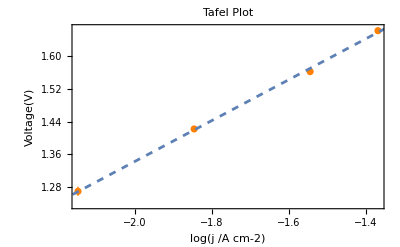

```mathematica
Show[ListPlot[addErrorInY[dataCPinCGlassyCarbon,errCPinGlassyCarbon],PlotStyle->Orange,Frame->True,FrameLabel->{"log(j /A cm-2)","Voltage(V)"},PlotLabel->"Tafel Plot"],Plot[lineCPGlassyCarbon[x],{x,0,-4},PlotStyle->Dashed]]
```

## pH 12.69

### LSV

```mathematica
ivsV1269 = changeTomA@makeIvList@(Import["/Users/alimalasmari/Desktop/Ali Alasmari mod8 Fall2023/Archive  20230927_140401 (0029)/LSV Experiment Fe_Ni OER pH 12.69 stir1000 pre-degredation/Voltammogram/Current vs Potential.csv"]);
```

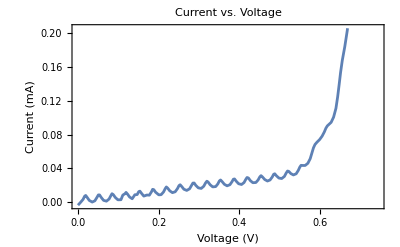

```mathematica
lsv1269=ListLinePlot[ivsV1269[[1;;150]],Frame->True,PlotLabel-> "Current vs. Voltage",FrameLabel->{"Voltage (V)","Current (mA)"}]
```

### CV

```mathematica
cp05ph1269=Import["/Users/alimalasmari/Desktop/Ali Alasmari mod8 Fall2023/Archive  20230927_140401 (0029)/CP Experiment Fe_Ni OER pH 12.69 0.5mA/Chronopotentiogram/Measured Potential.csv"][[52;;All]];
cp1ph1269=Import["/Users/alimalasmari/Desktop/Ali Alasmari mod8 Fall2023/Archive  20230927_140401 (0029)/CP Experiment Fe_Ni OER pH 12.69 1mA/Chronopotentiogram/Measured Potential.csv"][[52;;All]];
cp2ph1269=Import["/Users/alimalasmari/Desktop/Ali Alasmari mod8 Fall2023/Archive  20230927_140401 (0029)/CP Experiment Fe_Ni OER pH 12.69 2mA/Chronopotentiogram/Measured Potential.csv"][[52;;All]];
cp3ph1269=Import["/Users/alimalasmari/Desktop/Ali Alasmari mod8 Fall2023/Archive  20230927_140401 (0029)/CP Experiment Fe_Ni OER pH 12.69 3mA/Chronopotentiogram/Measured Potential.csv"][[52;;All]];
cp4ph1269=Import["/Users/alimalasmari/Desktop/Ali Alasmari mod8 Fall2023/Archive  20230927_140401 (0029)/CP Experiment Fe_Ni OER pH 12.69 4mA/Chronopotentiogram/Measured Potential.csv"][[52;;All]];
cp5ph1269=Import["/Users/alimalasmari/Desktop/Ali Alasmari mod8 Fall2023/Archive  20230927_140401 (0029)/CP Experiment Fe_Ni OER pH 12.69 5mA/Chronopotentiogram/Measured Potential.csv"][[52;;All]];
cpAllph1269 = {cp05ph1269,cp1ph1269,cp2ph1269,cp3ph1269,cp4ph1269,cp5ph1269};
```

```mathematica
ListPlot[cpAllph1269,PlotRange->{All,{0,All}},PlotLabels->{"0.50mA","1.00mA","2.00mA","3.00mA","4.00mA","5.00mA"},PlotLabel->"Potential vs. Time",Frame->True,FrameLabel->{"Time(s)","Potential(V)"}]
```

-Graphics-

### Tafel Analysis

```mathematica
cp1269mean=findMeanCP[cpAllph1269]
```

{0.739343,0.839643,1.0262,1.24229,1.47458,1.79064}

```mathematica
cp1269err=findErrCP[cpAllph1269]
```

{0.000282638,0.000427859,0.00269326,0.0140649,0.0144969,0.0445312}

```mathematica
cp1269err/cp1269mean
```

{0.000382282,0.000509572,0.00262449,0.0113217,0.00983122,0.0248689}

```mathematica
cp1269data = makeCPdata[cp1269mean];
```

```mathematica
cp1269Fit = modelFitCP[cp1269data,cp1269err];
```

```mathematica
NumberForm[cp1269Fit["ParameterTable"],3]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 1.5 | 0.00331 | 454. | 1.41×10^-10
x | 0.356 | 0.00161 | 221. | 2.5×10^-9

```mathematica
NumberForm[cp1269Fit["RSquared"],3]
```

0.956

```mathematica
cp1269line=makeFitExpression@extractFitParamters[cp1269Fit]
```

x (0.35610.0016)+(1.50230.0033)

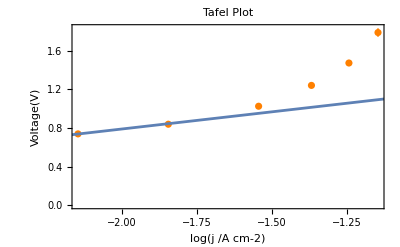

```mathematica
Show[ListPlot[addErrorInY[cp1269data,cp1269err],PlotStyle->Orange,Frame->True,FrameLabel->{"log(j /A cm-2)","Voltage(V)"},PlotLabel->"Tafel Plot"],Plot[cp1269Fit[x],{x,0,-4}]]
```

## pH 13

### LSV

```mathematica
ivsV13 = changeTomA@makeIvList@(Import["/Users/alimalasmari/Desktop/Ali Alasmari mod8 Fall2023/Archive  20230925_151912 (0001)/LSV Experiment Fe_Ni OER pH 13 zoom/Voltammogram/Current vs Potential.csv"]);
```

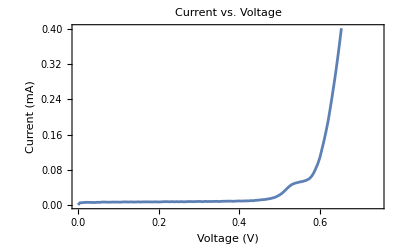

```mathematica
ListLinePlot[ivsV13[[1;;150]],Frame->True,PlotLabel-> "Current vs. Voltage",FrameLabel->{"Voltage (V)","Current (mA)"}]
```

### CP

```mathematica
cp05ph13=Import["/Users/alimalasmari/Desktop/Ali Alasmari mod8 Fall2023/Archive  20230925_151912 (0001)/CP Experiment Fe_Ni HER pH 13 0.5mA/Chronopotentiogram/Measured Potential.csv"][[52;;All]];
cp1ph13=Import["/Users/alimalasmari/Desktop/Ali Alasmari mod8 Fall2023/Archive  20230925_151912 (0001)/CP Experiment Fe_Ni HER pH 13 1mA/Chronopotentiogram/Measured Potential.csv"][[52;;All]];
cp2ph13=Import["/Users/alimalasmari/Desktop/Ali Alasmari mod8 Fall2023/Archive  20230925_151912 (0001)/CP Experiment Fe_Ni HER pH 13 2mA/Chronopotentiogram/Measured Potential.csv"][[52;;All]];
cp3ph13=Import["/Users/alimalasmari/Desktop/Ali Alasmari mod8 Fall2023/Archive  20230925_151912 (0001)/CP Experiment Fe_Ni HER pH 13 3mA/Chronopotentiogram/Measured Potential.csv"][[52;;All]];
cp4ph13=Import["/Users/alimalasmari/Desktop/Ali Alasmari mod8 Fall2023/Archive  20230925_151912 (0001)/CP Experiment Fe_Ni HER pH 13 4mA/Chronopotentiogram/Measured Potential.csv"][[52;;All]];
cp5ph13=Import["/Users/alimalasmari/Desktop/Ali Alasmari mod8 Fall2023/Archive  20230925_151912 (0001)/CP Experiment Fe_Ni HER pH 13 5mA/Chronopotentiogram/Measured Potential.csv"][[52;;All]];
cpAllph13 = {cp05ph13,cp1ph13,cp2ph13,cp3ph13,cp4ph13,cp5ph13};
```

```mathematica
ListPlot[cpAllph13,PlotRange->{All,{0,All}},PlotLabels->{"0.50mA","1.00mA","2.00mA","3.00mA","4.00mA","5.00mA"},PlotLabel->"Potential vs. Time",Frame->True,FrameLabel->{"Time(s)","Potential(V)"}]
```

-Graphics-

### Tafel Analysis

```mathematica
cp13mean=findMeanCP[cpAllph13]
```

{0.651948,0.717604,0.826108,0.942607,0.991827,1.11161}

```mathematica
cp13err=findErrCP[cpAllph13]
```

{0.0013734,0.00140166,0.00348521,0.00387747,0.023015,0.00838157}

```mathematica
cp13err/cp13mean
```

{0.00210661,0.00195325,0.00421883,0.00411356,0.0232047,0.00754001}

```mathematica
cp13data = makeCPdata[cp13mean];
```

```mathematica
cp13Fit = modelFitCP[cp13data,cp13err];
```

```mathematica
NumberForm[cp13Fit["ParameterTable"],3]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 1.37 | 0.00726 | 188. | 4.78×10^-9
x | 0.339 | 0.00375 | 90.6 | 8.91×10^-8

```mathematica
NumberForm[cp13Fit["RSquared"],3]
```

0.916

```mathematica
cp13line=makeFitExpression@extractFitParamters[cp13Fit]
```

x (0.3390.004)+(1.3660.007)

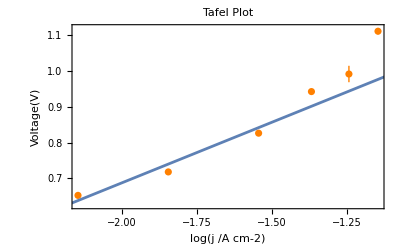

```mathematica
Show[ListPlot[addErrorInY[cp13data,cp13err],PlotStyle->Orange,Frame->True,FrameLabel->{"log(j /A cm-2)","Voltage(V)"},PlotLabel->"Tafel Plot"],Plot[cp13Fit[x],{x,0,-4}]]
```

### LSV of pH13 tried agian using the other catalyst

```mathematica
ivsV13v2 = changeTomA@makeIvList@(Import["/Users/alimalasmari/Desktop/Ali Alasmari mod8 Fall2023/Archive  20231002_142336 (0070)/LSV Experiment Fe_Ni OER pH 13 Stir/Voltammogram/Current vs Potential.csv"]);
```

```mathematica
ListLinePlot[{ivsV13v2[[1;;150]],ivsV13[[1;;150]]},Frame->True,PlotLabel-> "Current vs. Voltage",FrameLabel->{"Voltage (V)","Current (mA)"},PlotLabels->LineLegend[{Orange,Darker[Blue,0.3]},{"Catalyst 1","Catalyst 2"}],PlotStyle->{{Bold},{Orange,Dashed}}]
```

-Graphics-

```mathematica
ListLinePlot[{ivsV13v2,ivsV13},Frame->True,PlotLabel-> "Current vs. Voltage",FrameLabel->{"Voltage (V)","Current (mA)"},PlotLabels->LineLegend[{Orange,Darker[Blue,0.3]},{"Catalyst 1","Catalyst 2"}],PlotStyle->{{Bold},{Orange,Dashed}}]
```

-Graphics-

```mathematica
cp05ph13v2 = Import["/Users/alimalasmari/Desktop/Ali Alasmari mod8 Fall2023/Archive  20231002_142336 (0070)/CP Experiment Fe_Ni OER pH 13 0.5mA/Chronopotentiogram/Measured Potential.csv"][[52;;All]];
```

```mathematica
ListPlot[{cp05ph13v2,cp05ph13},PlotRange->{All,{0,All}},PlotLabels->{"Catalyst 2","Catalyst 1"},PlotLabel->"Potential vs. Time",Frame->True,PlotLabels->LineLegend[{Orange,Darker[Blue,0.3]},{"Catalyst 1","Catalyst 2"}]]
```

-Graphics-

```mathematica
0.5/areaElectrode
```

7.14286

```mathematica
findMeanCP[{cp05ph13v2,cp05ph13}]
```

{0.709161,0.651948}

```mathematica
findErrCP[{cp05ph13v2,cp05ph13}]
```

{0.00115035,0.0013734}

## pH 13.30

### LSV

```mathematica
ivsV1330= changeTomA@makeIvList@(Import["/Users/alimalasmari/Desktop/Ali Alasmari mod8 Fall2023/Archive  20231002_142336 (0070)/LSV Experiment Fe_Ni OER pH 13.30/Voltammogram/Current vs Potential.csv"]);
```

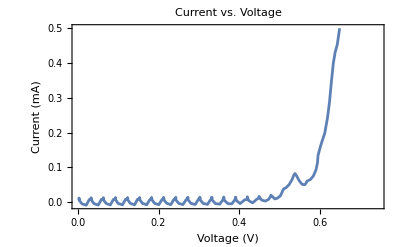

```mathematica
ListLinePlot[ivsV1330[[1;;150]],Frame->True,PlotLabel-> "Current vs. Voltage",FrameLabel->{"Voltage (V)","Current (mA)"}]
```

### CP

```mathematica
cp05ph1330=Import["/Users/alimalasmari/Desktop/Ali Alasmari mod8 Fall2023/Archive  20231002_142336 (0070)/CP Experiment Fe_Ni OER pH 13.30 0.5mA/Chronopotentiogram/Measured Potential.csv"][[52;;All]];
cp1ph1330=Import["/Users/alimalasmari/Desktop/Ali Alasmari mod8 Fall2023/Archive  20231002_142336 (0070)/CP Experiment Fe_Ni OER pH 13.30 1mA/Chronopotentiogram/Measured Potential.csv"][[52;;All]];
cp2ph1330=Import["/Users/alimalasmari/Desktop/Ali Alasmari mod8 Fall2023/Archive  20231002_142336 (0070)/CP Experiment Fe_Ni OER pH 13.30 2mA/Chronopotentiogram/Measured Potential.csv"][[52;;All]];
cp3ph1330=Import["/Users/alimalasmari/Desktop/Ali Alasmari mod8 Fall2023/Archive  20231002_142336 (0070)/CP Experiment Fe_Ni OER pH 13.30 3mA/Chronopotentiogram/Measured Potential.csv"][[52;;All]];
cp4ph1330=Import["/Users/alimalasmari/Desktop/Ali Alasmari mod8 Fall2023/Archive  20231002_142336 (0070)/CP Experiment Fe_Ni OER pH 13.30 4mA/Chronopotentiogram/Measured Potential.csv"][[52;;All]];
cp5ph1330=Import["/Users/alimalasmari/Desktop/Ali Alasmari mod8 Fall2023/Archive  20231002_142336 (0070)/CP Experiment Fe_Ni OER pH 13.30 5mA/Chronopotentiogram/Measured Potential.csv"][[52;;All]];
cpAllph1330 = {cp05ph1330,cp1ph1330,cp2ph1330,cp3ph1330,cp4ph1330,cp5ph1330};
```

```mathematica
ListPlot[cpAllph1330,PlotRange->{All,{0,All}},PlotLabels->{"0.50mA","1.00mA","2.00mA","3.00mA","4.00mA","5.00mA"},PlotLabel->"Potential vs. Time",Frame->True,FrameLabel->{"Time(s)","Potential(V)"}]
```

-Graphics-

### Tafel Analysis

```mathematica
cp1330mean=findMeanCP[cpAllph1330]
```

{0.656537,0.714119,0.812424,0.905397,1.01682,1.15035}

```mathematica
cp1330err=findErrCP[cpAllph1330]
```

{0.000984593,0.000964422,0.00193233,0.0063776,0.00905218,0.0110479}

```mathematica
cp1330err/cp1330mean
```

{0.00149967,0.00135051,0.00237848,0.00704398,0.00890247,0.00960391}

```mathematica
cp1330data = makeCPdata[cp1330mean];
```

```mathematica
cp1330Fit = modelFitCP[cp1330data,cp1330err];
```

```mathematica
NumberForm[cp1330Fit["ParameterTable"],3]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 1.23 | 0.00574 | 214. | 2.87×10^-9
x | 0.271 | 0.00296 | 91.6 | 8.51×10^-8

```mathematica
NumberForm[cp1330Fit["RSquared"],3]
```

0.893

```mathematica
cp1330line=makeFitExpression@extractFitParamters[cp1330Fit]
```

x (0.27090.0030)+(1.2280.006)

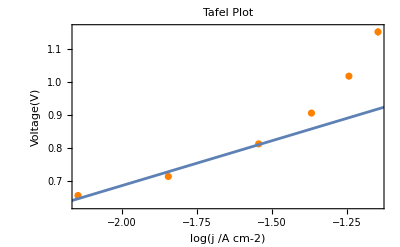

```mathematica
Show[ListPlot[addErrorInY[cp1330data,cp1330err],PlotStyle->Orange,Frame->True,FrameLabel->{"log(j /A cm-2)","Voltage(V)"},PlotLabel->"Tafel Plot"],Plot[cp1330Fit[x],{x,0,-4}]]
```

## pH 13.69

### LSV

```mathematica
ivsV1369 = changeTomA@makeIvList@(Import["/Users/alimalasmari/Desktop/Ali Alasmari mod8 Fall2023/Archive  20230927_140401 (0029)/LSV Experiment Fe_Ni OER pH 13.69 stir1000/Voltammogram/Current vs Potential.csv"]);
```

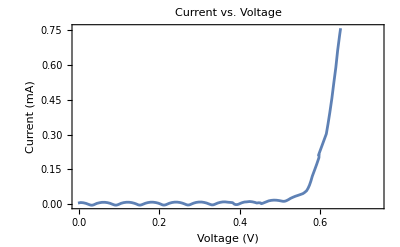

```mathematica
ListLinePlot[ivsV1369[[1;;150]],Frame->True,PlotLabel-> "Current vs. Voltage",FrameLabel->{"Voltage (V)","Current (mA)"}]
```

### CP

```mathematica
cp05ph1369=Import["/Users/alimalasmari/Desktop/Ali Alasmari mod8 Fall2023/Archive  20230927_140401 (0029)/CP Experiment Fe_Ni OER pH 13.69 0.5mA/Chronopotentiogram/Measured Potential.csv"][[52;;All]];
cp1ph1369=Import["/Users/alimalasmari/Desktop/Ali Alasmari mod8 Fall2023/Archive  20230927_140401 (0029)/CP Experiment Fe_Ni OER pH 13.69 1mA/Chronopotentiogram/Measured Potential.csv"][[52;;All]];
cp2ph1369=Import["/Users/alimalasmari/Desktop/Ali Alasmari mod8 Fall2023/Archive  20230927_140401 (0029)/CP Experiment Fe_Ni OER pH 13.69 2mA/Chronopotentiogram/Measured Potential.csv"][[52;;All]];
cp3ph1369=Import["/Users/alimalasmari/Desktop/Ali Alasmari mod8 Fall2023/Archive  20230927_140401 (0029)/CP Experiment Fe_Ni OER pH 13.69 3mA/Chronopotentiogram/Measured Potential.csv"][[52;;All]];
cp4ph1369=Import["/Users/alimalasmari/Desktop/Ali Alasmari mod8 Fall2023/Archive  20230927_140401 (0029)/CP Experiment Fe_Ni OER pH 13.69 4mA/Chronopotentiogram/Measured Potential.csv"][[52;;All]];
cp5ph1369=Import["/Users/alimalasmari/Desktop/Ali Alasmari mod8 Fall2023/Archive  20230927_140401 (0029)/CP Experiment Fe_Ni OER pH 13.69 5mA/Chronopotentiogram/Measured Potential.csv"][[52;;All]];
cpAllph1369 = {cp05ph1369,cp1ph1369,cp2ph1369,cp3ph1369,cp4ph1369,cp5ph1369};
```

```mathematica
ListPlot[cpAllph1369,PlotRange->{All,{0,All}},PlotLabels->{"0.50mA","1.00mA","2.00mA","3.00mA","4.00mA","5.00mA"},PlotLabel->"Potential vs. Time",Frame->True,FrameLabel->{"Time(s)","Potential(V)"}]
```

-Graphics-

### Tafel Analysis

```mathematica
cp1369mean=findMeanCP[cpAllph1369]
```

{0.625514,0.670876,0.741629,0.809843,0.886349,0.966156}

```mathematica
cp1369err=findErrCP[cpAllph1369]
```

{0.00031967,0.000302309,0.00135276,0.00347937,0.00587473,0.0102856}

```mathematica
cp1369err/cp1369mean
```

{0.000511051,0.000450618,0.00182405,0.00429635,0.00662801,0.0106459}

```mathematica
cp1369data = makeCPdata[cp1369mean];
```

```mathematica
cp1369Fit = modelFitCP[cp1369data,cp1369err];
```

```mathematica
NumberForm[cp1369Fit["ParameterTable"],3]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.992 | 0.0025 | 396. | 2.43×10^-10
x | 0.172 | 0.00126 | 136. | 1.75×10^-8

```mathematica
NumberForm[cp1369Fit["RSquared"],3]
```

0.939

```mathematica
cp1369line=makeFitExpression@extractFitParamters[cp1369Fit]
```

x (0.17210.0013)+(0.99240.0025)

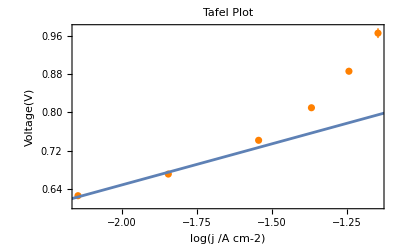

```mathematica
Show[ListPlot[addErrorInY[cp1369data,cp1369err],PlotStyle->Orange,Frame->True,FrameLabel->{"log(j /A cm-2)","Voltage(V)"},PlotLabel->"Tafel Plot"],Plot[cp1369Fit[x],{x,0,-4}]]
```

## pH 14

#### LSV

```mathematica
ivsV14 = changeTomA@makeIvList@(Import["/Users/alimalasmari/Desktop/Ali Alasmari mod8 Fall2023/Archive  20230925_151912 (0001)/LSV Experiment Fe_Ni OER pH 14/experiment/results/Current vs Potential.csv"]);
```

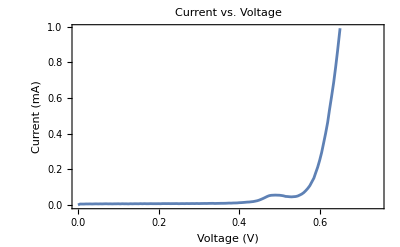

```mathematica
ListLinePlot[ivsV14[[1;;150]],Frame->True,PlotLabel-> "Current vs. Voltage",FrameLabel->{"Voltage (V)","Current (mA)"}]
```

```mathematica
lsv14=ListLinePlot[ivsV14,Frame->True,PlotLabel-> "Current vs. Voltage",FrameLabel->{"Voltage (V)","Current (mA)"}];
```

#### CP

Note: when naming the files for this part I read the current wrong and assumed I was doing HER and planed on discarding the data. Later, I realized that data is fine and the current is the right sign, so I used it but kept the names.

```mathematica
cp05ph14=Import["/Users/alimalasmari/Desktop/Ali Alasmari mod8 Fall2023/Archive  20230925_151912 (0001)/CP Experiment Fe_Ni HER pH 14 0.5mA/Chronopotentiogram/Measured Potential.csv"][[52;;All]];
cp1ph14=Import["/Users/alimalasmari/Desktop/Ali Alasmari mod8 Fall2023/Archive  20230925_151912 (0001)/CP Experiment Fe_Ni HER pH 14 1mA/Chronopotentiogram/Measured Potential.csv"][[52;;All]];
cp2ph14=Import["/Users/alimalasmari/Desktop/Ali Alasmari mod8 Fall2023/Archive  20230925_151912 (0001)/CP Experiment Fe_Ni HER pH 14 2mA/Chronopotentiogram/Measured Potential.csv"][[52;;All]];
cp3ph14=Import["/Users/alimalasmari/Desktop/Ali Alasmari mod8 Fall2023/Archive  20230925_151912 (0001)/CP Experiment Fe_Ni HER pH 14 3mA/Chronopotentiogram/Measured Potential.csv"][[52;;All]];
cp4ph14=Import["/Users/alimalasmari/Desktop/Ali Alasmari mod8 Fall2023/Archive  20230925_151912 (0001)/CP Experiment Fe_Ni HER pH 14 4mA/Chronopotentiogram/Measured Potential.csv"][[52;;All]];
cp5ph14=Import["/Users/alimalasmari/Desktop/Ali Alasmari mod8 Fall2023/Archive  20230925_151912 (0001)/CP Experiment Fe_Ni HER pH 14 5mA/Chronopotentiogram/Measured Potential.csv"][[52;;All]];
cpAllph14 = {cp05ph14,cp1ph14,cp2ph14,cp3ph14,cp4ph14,cp5ph14};
```

```mathematica
ListPlot[cpAllph14,PlotRange->{All,{0,All}},PlotLabels->{"0.50mA","1.00mA","2.00mA","3.00mA","4.00mA","5.00mA"},PlotLabel->"Potential vs. Time",Frame->True,FrameLabel->{"Time(s)","Potential(V)"}]
```

-Graphics-

#### Tafel Analysis

```mathematica
cp14mean=findMeanCP[cpAllph14]
```

{0.588967,0.623953,0.674959,0.717986,0.760437,0.801329}

```mathematica
cp14err=findErrCP[cpAllph14]
```

{0.000637552,0.000510564,0.00285758,0.00129508,0.00150646,0.00340546}

```mathematica
cp14err/cp14mean
```

{0.00108249,0.000818273,0.00423371,0.00180376,0.00198104,0.00424976}

```mathematica
cp14data = makeCPdata[cp14mean];
```

```mathematica
cp14Fit = modelFitCP[cp14data,cp14err];
```

```mathematica
NumberForm[cp14Fit["ParameterTable"],3]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.963 | 0.00249 | 387. | 2.66×10^-10
x | 0.179 | 0.00132 | 135. | 1.8×10^-8

```mathematica
NumberForm[cp14Fit["RSquared"],3]
```

0.953

```mathematica
cp14line=makeFitExpression@extractFitParamters[cp14Fit]
```

x (0.17890.0013)+(0.96320.0025)

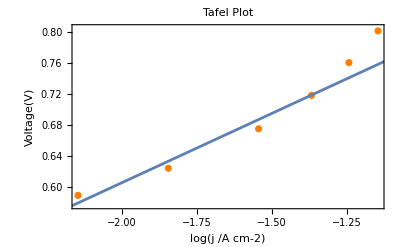

```mathematica
Show[ListPlot[addErrorInY[cp14data,cp14err],PlotStyle->Orange,Frame->True,FrameLabel->{"log(j /A cm-2)","Voltage(V)"},PlotLabel->"Tafel Plot"],Plot[cp14Fit[x],{x,0,-4}]]
```

## pH 14.30

### LSV

```mathematica
ivsV1430= changeTomA@makeIvList@(Import["/Users/alimalasmari/Desktop/Ali Alasmari mod8 Fall2023/Archive  20231002_142336 (0070)/LSV Experiment Fe_Ni OER pH 14.30/Voltammogram/Current vs Potential.csv"]);
```

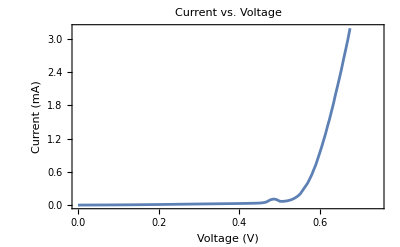

```mathematica
ListLinePlot[ivsV1430[[1;;150]],Frame->True,PlotLabel-> "Current vs. Voltage",FrameLabel->{"Voltage (V)","Current (mA)"}]
```

### CP

```mathematica
cp05ph1430=Import["/Users/alimalasmari/Desktop/Ali Alasmari mod8 Fall2023/Archive  20231002_142336 (0070)/CP Experiment Fe_Ni OER pH 14.30 0.5mA/Chronopotentiogram/Measured Potential.csv"][[52;;All]];
cp1ph1430=Import["/Users/alimalasmari/Desktop/Ali Alasmari mod8 Fall2023/Archive  20231002_142336 (0070)/CP Experiment Fe_Ni OER pH 14.30 1mA/Chronopotentiogram/Measured Potential.csv"][[52;;All]];
cp2ph1430=Import["/Users/alimalasmari/Desktop/Ali Alasmari mod8 Fall2023/Archive  20231002_142336 (0070)/CP Experiment Fe_Ni OER pH 14.30 2mA/Chronopotentiogram/Measured Potential.csv"][[52;;All]];
cp3ph1430=Import["/Users/alimalasmari/Desktop/Ali Alasmari mod8 Fall2023/Archive  20231002_142336 (0070)/CP Experiment Fe_Ni OER pH 14.30 3mA/Chronopotentiogram/Measured Potential.csv"][[52;;All]];
cp4ph1430=Import["/Users/alimalasmari/Desktop/Ali Alasmari mod8 Fall2023/Archive  20231002_142336 (0070)/CP Experiment Fe_Ni OER pH 14.30 4mA/Chronopotentiogram/Measured Potential.csv"][[52;;All]];
cp5ph1430=Import["/Users/alimalasmari/Desktop/Ali Alasmari mod8 Fall2023/Archive  20231002_142336 (0070)/CP Experiment Fe_Ni OER pH 14.30 5mA/Chronopotentiogram/Measured Potential.csv"][[52;;All]];
cpAllph1430 = {cp05ph1430,cp1ph1430,cp2ph1430,cp3ph1430,cp4ph1430,cp5ph1430};
```

```mathematica
ListPlot[cpAllph1430,PlotRange->{All,{0,All}},PlotLabels->{"0.50mA","1.00mA","2.00mA","3.00mA","4.00mA","5.00mA"},PlotLabel->"Potential vs. Time",Frame->True,FrameLabel->{"Time(s)","Potential(V)"}]
```

-Graphics-

### Tafel Analysis

```mathematica
cp1430mean=findMeanCP[cpAllph1430]
```

{0.586159,0.625227,0.680745,0.733397,0.786145,0.849886}

```mathematica
cp1430err=findErrCP[cpAllph1430]
```

{0.000968253,0.000780652,0.00150305,0.00301046,0.00395334,0.00901088}

```mathematica
cp1430err/cp1430mean
```

{0.00165186,0.00124859,0.00220795,0.00410482,0.00502877,0.0106025}

```mathematica
cp1430data = makeCPdata[cp1430mean];
```

```mathematica
cp1430Fit = modelFitCP[cp1430data,cp1430err];
```

```mathematica
NumberForm[cp1430Fit["ParameterTable"],3]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.964 | 0.00434 | 222. | 2.46×10^-9
x | 0.18 | 0.0023 | 78.2 | 1.6×10^-7

```mathematica
NumberForm[cp1430Fit["RSquared"],3]
```

0.935

```mathematica
cp1430line=makeFitExpression@extractFitParamters[cp1430Fit]
```

x (0.18000.0023)+(0.9640.004)

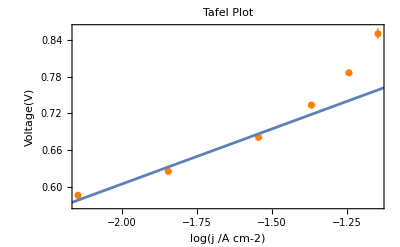

```mathematica
Show[ListPlot[addErrorInY[cp1430data,cp1430err],PlotStyle->Orange,Frame->True,FrameLabel->{"log(j /A cm-2)","Voltage(V)"},PlotLabel->"Tafel Plot"],Plot[cp1430Fit[x],{x,0,-4}]]
```

## Fit of Slope over pH

```mathematica
tafelData={{12.69,0.356,0.002},{13,0.339,0.004},{13.3,0.271,0.003},{13.69,0.172,0.001},{14,0.179,0.001},{14.3,0.18,0.002}};
```

```mathematica
tafelFit= LinearModelFit[tafelData[[All,1;;2]], x,x,Weights->1/(tafelData[[All,3]]^2),VarianceEstimatorFunction->(1&)];
```

```mathematica
NumberForm[tafelFit["ParameterTable"],3]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 1.85 | 0.0198 | 93.4 | 7.89×10^-8
x | -0.12 | 0.00144 | -83.3 | 1.24×10^-7

```mathematica
NumberForm[tafelFit["RSquared"],3]
```

0.756

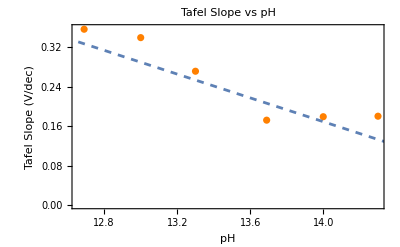

```mathematica
Show[ListPlot[addErrorInY[tafelData[[All,1;;2]],tafelData[[All,3]]],PlotStyle->Orange,Frame->True,FrameLabel->{"pH","Tafel Slope (V/dec)"},PlotLabel->"Tafel Slope vs pH"],Plot[tafelFit[x],{x,10,15},PlotStyle->Dashed]]
```

### Compare the two catalysts at pH 14 CV of glassy carbon and LSV

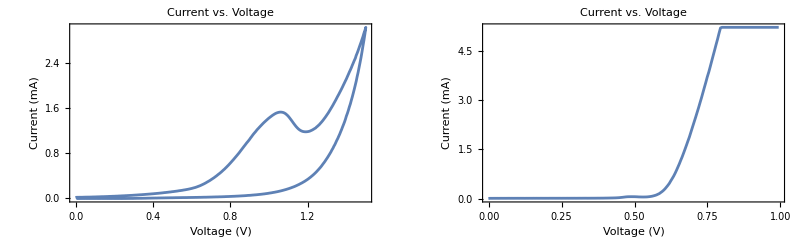

```mathematica
GraphicsGrid[{{cvgc,lsv14}}]
```